# Robot sferico del I tipo

## Cinematica diretta 3DOF

```mathematica
tab={{Subscript[q, 1],Subscript[L, 1],Pi/2,0},{Subscript[q, 2],0, Pi/2, Subscript[L, 2]},{0,Subscript[q, 3],0,0}};
TableForm[tab,TableHeadings->{{"1","2","3"},{"θ","d","α","a","x","y","z"}}]
```

| θ | d | α | a
1 | q_1 | L_1 | π/2 | 0
2 | q_2 | 0 | π/2 | L_2
3 | 0 | q_3 | 0 | 0

```mathematica
Q03=cinematicaDiretta[tab];
h03=Q03[[1;;3,4]];
Q03/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]}//MatrixForm
```

(c_1 c_2 | s_1 | c_1 s_2 | c_1 (c_2 L_2+q_3 s_2)
c_2 s_1 | -c_1 | s_1 s_2 | s_1 (c_2 L_2+q_3 s_2)
s_2 | 0 | -c_2 | L_1-c_2 q_3+L_2 s_2
0 | 0 | 0 | 1)

## Cinematica diretta 6 DOF

```mathematica
tab2={{Subscript[q, 1],Subscript[L, 1],Pi/2,0},{Subscript[q, 2],0, Pi/2, Subscript[L, 2]},{0,Subscript[q, 3],0,0},{Subscript[q, 4],Subscript[L, 4],-Pi/2,0},{Subscript[q, 5],0,Pi/2,0},{Subscript[q, 6],Subscript[L, 6],0,0}};
tab2//MatrixForm
```

(q_1 | L_1 | π/2 | 0
q_2 | 0 | π/2 | L_2
0 | q_3 | 0 | 0
q_4 | L_4 | -π/2 | 0
q_5 | 0 | π/2 | 0
q_6 | L_6 | 0 | 0)

```mathematica
cinematicaDiretta[tab2]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]}//MatrixForm
```

(s_1 (c_5 c_6 s_4+c_4 s_6)+c_1 (-c_6 s_2 s_5+c_2 (c_4 c_5 c_6-s_4 s_6)) | c_6 (c_4 s_1-c_1 c_2 s_4)-(c_5 s_1 s_4+c_1 (c_2 c_4 c_5-s_2 s_5)) s_6 | s_1 s_4 s_5+c_1 (c_5 s_2+c_2 c_4 s_5) | c_1 c_2 L_2+c_1 (L_4+c_5 L_6+q_3) s_2+c_1 c_2 c_4 L_6 s_5+L_6 s_1 s_4 s_5
c_6 (c_5 (c_2 c_4 s_1-c_1 s_4)-s_1 s_2 s_5)-(c_1 c_4+c_2 s_1 s_4) s_6 | c_1 (-c_4 c_6+c_5 s_4 s_6)-s_1 (-s_2 s_5 s_6+c_2 (c_6 s_4+c_4 c_5 s_6)) | c_5 s_1 s_2+(c_2 c_4 s_1-c_1 s_4) s_5 | c_2 L_2 s_1+(L_4+c_5 L_6+q_3) s_1 s_2+c_2 c_4 L_6 s_1 s_5-c_1 L_6 s_4 s_5
c_6 (c_4 c_5 s_2+c_2 s_5)-s_2 s_4 s_6 | -c_6 s_2 s_4-(c_4 c_5 s_2+c_2 s_5) s_6 | -c_2 c_5+c_4 s_2 s_5 | L_1-c_2 (L_4+c_5 L_6+q_3)+s_2 (L_2+c_4 L_6 s_5)
0 | 0 | 0 | 1)

## Cinematica inversa

```mathematica
{e1,e2,e3}=TrigExpand[{x,y,z}-h03]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]};
e4=Subscript[c, 1]^2+Subscript[s, 1]^2-1;
e5=Subscript[c, 2]^2+Subscript[s, 2]^2-1;
TableForm[{e1,e2,e3}]
```

x-c_1 c_2 L_2-c_1 q_3 s_2
y-c_2 L_2 s_1-q_3 s_1 s_2
z-L_1+c_2 q_3-L_2 s_2

### Calcolo q_3

```mathematica
sol=GroebnerBasis[{e1,e2,e3,e4,e5},{Subscript[q, 3]},{Subscript[c, 1],Subscript[s, 1],Subscript[c, 2],Subscript[s, 2]},CoefficientDomain->RationalFunctions]
Solve[sol==0, {Subscript[q, 3]}]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2}//FullSimplify
```

{-x^2-y^2-z^2+2 z L_1-L_1^2+L_2^2+q_3^2}

{{q_3→-√(-l2^2+x^2+y^2+(l1-z)^2)},{q_3→√(-l2^2+x^2+y^2+(l1-z)^2)}}

```mathematica
(*Segue dunque che x^2+y^2+(l1-z)^2≥l2^2 *)
```

### Calcolo q_2

```mathematica
(*Calcolo Subscript[q, 2]*)
sol=GroebnerBasis[{e1,e2,e3,e5},{Subscript[c, 2],Subscript[s, 2]},{Subscript[c, 1],Subscript[s, 1]},CoefficientDomain->RationalFunctions];
sol//TableForm
Solve[sol[[1]]==0,Subscript[s, 2]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[q, 3]->q3,Subscript[s, 2]->s2}//FullSimplify
Solve[sol[[2]]==0,Subscript[c, 2]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[q, 3]->q3,Subscript[s, 2]->s2}//FullSimplify
```

z^2-2 z L_1+L_1^2-q_3^2+(-2 z L_2+2 L_1 L_2) s_2+(L_2^2+q_3^2) s_2^2
z-L_1+c_2 q_3-L_2 s_2

{{s2→-(l1 l2+√(q3^2 (l2^2+q3^2-(l1-z)^2))-l2 z)/(l2^2+q3^2)},{s2→(-l1 l2+√(q3^2 (l2^2+q3^2-(l1-z)^2))+l2 z)/(l2^2+q3^2)}}

{{c_2→(l1+l2 s2-z)/q3}}

```mathematica
q3^2 (l2^2+q3^2-(l1-z)^2)/.{q3->√(-l2^2+x^2+y^2+(l1-z)^2)}//FullSimplify
```

(x^2+y^2) (-l2^2+x^2+y^2+(l1-z)^2)

```mathematica
(*Segue dunque che x^2+y^2+(l1-z)^2≥l2^2(condizione già trovata per Subscript[q, 3])*)
```

#### q_3==0, L_2≠0

```mathematica
TableForm[{e1,e2,e3}]/.{Subscript[q, 3]->0}
```

x-c_1 c_2 L_2
y-c_2 L_2 s_1
z-L_1-L_2 s_2

```mathematica
sol=GroebnerBasis[{e1,e2,e4},{Subscript[c, 2]},{Subscript[c, 1],Subscript[s, 1]},CoefficientDomain->RationalFunctions]/.{Subscript[q, 3]->0}
```

{x^2+y^2-c_2^2 L_2^2}

```mathematica
Solve[sol==0,Subscript[c, 2]]/.{Subscript[L, 2]->l2}
```

{{c_2→-(√(x^2+y^2))/l2},{c_2→(√(x^2+y^2))/l2}}

#### q_3==0, L_2==0

```mathematica
(*Calcolo Subscript[c, 2] se Subscript[q, 3]==0 e Subscript[L, 2]==0*)
TableForm[{e1,e2,e3}]/.{Subscript[q, 3]->0,Subscript[L, 2]->0}
```

x
y
z-L_1

```mathematica
(*Segue dunque che se Subscript[q, 3]==0 e Subscript[L, 2]==0 Subscript[q, 2] è arbitrario*)
```

### Calcolo q_1

```mathematica
e1//FullSimplify
e2//FullSimplify
```

x-c_1 (c_2 L_2+q_3 s_2)

y-s_1 (c_2 L_2+q_3 s_2)

```mathematica
Solve[{e1,e2}==0,{Subscript[c, 1],Subscript[s, 1]}]/.{Subscript[c, 2]->c2,Subscript[s, 2]->s2,Subscript[L, 2]->l2,Subscript[q, 3]->q3}
```

{{c_1→x/(c2 l2+q3 s2),s_1→y/(c2 l2+q3 s2)}}

#### (c_2 L_2 + q_3 s_2) == 0

```mathematica
Assuming[(Subscript[c, 2] Subscript[L, 2]+Subscript[q, 3] Subscript[s, 2])==0, TableForm[{e1,e2,e3}//FullSimplify]]
```

x
y
z-L_1+c_2 q_3-L_2 s_2

```mathematica
(*In tal caso Subscript[q, 1] è arbitrario*)
```

### Procedura

```mathematica
(*Questa procedura calcola le variabili di giunto corrispondenti alla posizione dell’end effector {x,y,z} fornita in ingresso.
I parametri l1 e l2 rappresentano le lunghezze dei segmenti Subscript[L, 1] e Subscript[L, 2] del robot,mentre g2 e g3, pari a ±1, permettono di scegliere una tra le diverse configurazioni ammissibili*)cinInversaSferico[x_,y_,z_,l1_,l2_,g2_,g3_]:=Module[{q1,q2,q3,c1,s1,c2,s2},
If[AllTrue[{x,y,z,l1,l2},numeroReale]&&(g2===1 || g2===-1)&&(g3===1 || g3===-1),
If[TrueQ[Refine[FullSimplify[x^2+y^2+(z-l1)^2-l2^2]>=0]],

q3=g3 √(-l2^2+x^2+y^2+(l1-z)^2)//FullSimplify;

If[N[q3]=!=0.,
s2=(-l1 l2+g2 √(q3^2 (l2^2+q3^2-(l1-z)^2))+l2 z)/(l2^2+q3^2);
c2=(l1+l2 s2-z)/q3;
q2=ArcTan[c2,s2]//FullSimplify;,

If[N[FullSimplify[l2]]=!=0.,
s2=(-l1 l2+g2 √(q3^2 (l2^2+q3^2-(l1-z)^2))+l2 z)/(l2^2+q3^2);
c2=g2(√(x^2+y^2))/l2;
q2=ArcTan[c2,s2]//FullSimplify;,

q2=0;(*Se q3==0 e l2==0 q2 è arbitrario*)]];


If[N[FullSimplify[c2 l2+q3 s2]]=!=0.,
c1=x/(c2 l2+q3 s2);
s1=y/(c2 l2+q3 s2);
q1=ArcTan[c1,s1]//FullSimplify;,

q1=0;(*Se (Subscript[c, 2] Subscript[l, 2]+Subscript[q, 3] Subscript[s, 2])==0 Subscript[q, 1] è arbitrario*)];


{q1,q2,q3},
Echo[{},"Il punto indicato è all'infuori dello spazio operativo"];],
Echo["Argomenti non validi"];
 ]]
```

## Test cinematica inversa

```mathematica
Q1=1;
Q2=3;
Q3=3;
L1=1;
L2=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
Echo[{xx,yy,zz},"Coordinate:"];
```

Coordinate:  {-0.841048,-1.30985,4.25222}

```mathematica
Echo[cinInversaSferico[xx,yy,zz,L1,L2,+1,+1],"gomito ++"];
Echo[cinInversaSferico[xx,yy,zz,L1,L2,+1,-1],"gomito +-"];
Echo[cinInversaSferico[xx,yy,zz,L1,L2,-1,+1],"gomito -+"];
Echo[cinInversaSferico[xx,yy,zz,L1,L2,-1,-1], "gomito --"];
```

gomito ++  {-2.14159,2.10718,3.}

gomito +-  {1.,1.03441,-3.}

gomito -+  {1.,3.,3.}

gomito --  {-2.14159,0.141593,-3.}

```mathematica
(*Da notare che la configurazione gomito -+ mi restituisce le variabili di giunto iniziali*)
```

## Rappresentazione grafica

```mathematica
(*Questa funzione disegna lo spazio operativo del robot antropomorfo, che corrisponde alla superficie ed allo spazio esterno di una sfera centrata in (0,0,l1) di raggio l2. I parametri dimX,dimY e dimZ indicano la dimensione (rispettivamente lungo x,y,z) del plot*)
soSferico[l1_,l2_,dimX_,dimY_,dimZ_]:=Module[{plot},
If[AllTrue[{l1,l2,dimX,dimY,dimZ},NumericQ[#]&&!parteComplessa[#]&]&&AllTrue[{dimX,dimY,dimZ},Positive],
plot=ContourPlot3D[x^2+y^2+(z-l1)^2==l2^2,{x,-dimX,dimX},{y,-dimY,dimY},{z,l1-dimZ,l1+dimZ},ContourStyle->Opacity[0.1,Blue],AxesLabel->{"x","y","z"}],
Echo["Argomenti non validi"];
]]
```

```mathematica
(*Andiamo ora a disegnare il robot*)
cinematicaDiretta[{tab[[1]]}]/.{Subscript[L, 1]->l1}//MatrixForm
cinematicaDiretta[tab[[1;;2]]]/.{Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[L, 1]->l1,Subscript[L, 2]->l2}//MatrixForm
cinematicaDiretta[tab]/.{Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[q, 3]->q3,Subscript[L, 1]->l1,Subscript[L, 2]->l2}//MatrixForm
```

(Cos[q_1] | 0 | Sin[q_1] | 0
Sin[q_1] | 0 | -Cos[q_1] | 0
0 | 1 | 0 | l1
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2] | Sin[q1] | Cos[q1] Sin[q2] | l2 Cos[q1] Cos[q2]
Cos[q2] Sin[q1] | -Cos[q1] | Sin[q1] Sin[q2] | l2 Cos[q2] Sin[q1]
Sin[q2] | 0 | -Cos[q2] | l1+l2 Sin[q2]
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2] | Sin[q1] | Cos[q1] Sin[q2] | Cos[q1] (l2 Cos[q2]+q3 Sin[q2])
Cos[q2] Sin[q1] | -Cos[q1] | Sin[q1] Sin[q2] | Sin[q1] (l2 Cos[q2]+q3 Sin[q2])
Sin[q2] | 0 | -Cos[q2] | l1-q3 Cos[q2]+l2 Sin[q2]
0 | 0 | 0 | 1)

```mathematica
(*Questa procedura rappresenta il robot sferico nello spazio. I parametri q1,q2 e q3 costituiscono le variabili di giunto del robot,l1 e l2 rappresentano le lunghezze dei segmenti Subscript[L, 1] e Subscript[L, 2],mentre dimX,dimY e dimZ definiscono le dimensioni del plot.*)robotSferico[q1_,q2_,q3_,l1_,l2_,dimX_,dimY_,dimZ_]:=Module[{x1,y1,z1,x2,y2,z2,x3,y3,z3,list, plot},
If[AllTrue[{q1,q2,q3,l1,l2,dimX,dimY,dimZ},NumericQ[#]&&!parteComplessa[#]&]&&AllTrue[{dimX,dimY,dimZ},Positive],

x1=0;
y1=0;
z1=l1;

x2=l2 Cos[q1] Cos[q2];
y2=l2 Cos[q2] Sin[q1];
z2=l1+l2 Sin[q2];

x3=Cos[q1] (l2 Cos[q2]+q3 Sin[q2]);
y3=Sin[q1] (l2 Cos[q2]+q3 Sin[q2]);
z3=l1-q3 Cos[q2]+l2 Sin[q2];

list={{0,0,0},{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}};
plot = ListLinePlot3D[list, PlotRange->{{-dimX,dimX},{-dimY,dimY},{l1-dimZ,l1+dimZ}},PlotStyle->{Red,Thick},AxesLabel->{"x","y","z"}],

Echo["Argomenti non validi"];]
]
```

## Raggiungimento di un punto arbitrario

```mathematica
(*Questa procedura rappresenta graficamente il robot con l’end effector posizionato nel punto (x,y,z). Prende in ingresso le lunghezze del robot l1 e l2, i suoi gomiti g2 e g3 ed una stringa s che specifica il titolo del grafico restituito in uscita*)
disegnoSferico[x_,y_,z_,l1_,l2_,g2_,g3_,s_]:=Module[{res,dimX,dimZ,p1,p2,p3},
If[StringQ[s],
res=cinInversaSferico[x,y,z,l1,l2,g2,g3];
If[!MatchQ[res,{_,_,_}],Abort[]];(*Argomenti non validi*)
Echo[res,s];

dimX=Abs[l2]+Abs[res[[3]]]+1;
dimZ=Abs[l1]+dimX;

p1=robotSferico[res[[1]],res[[2]],res[[3]],l1,l2,dimX,dimX,dimZ];
If[!MatchQ[p1,_Graphics3D],Abort[]];(*Argomenti non validi*)
p2=ListPointPlot3D[{{x,y,z}},PlotStyle->Green];
p3 = soSferico[l1,l2,dimX,dimX,dimZ];
Show[p1,p2,p3, PlotLabel->s],

Echo["Argomenti non validi"];]
]
```

```mathematica
(*Questa procedura rappresenta il robot mentre raggiunge il punto desiderato (x,y,z) in tutte le configurazioni cinematiche possibili.I parametri l1 e l2 indicano le lunghezze dei segmenti del robot.*)
raggPuntoSferico[x_,y_,z_,l1_,l2_]:=Module[{p1,p2,p3,p4},
Echo[{x,y,z}, "Coordinate"];
p1=disegnoSferico[x,y,z,l1,l2,+1,+1,"Gomito ++"];
If[!MatchQ[p1,_Graphics3D],Abort[]];
p2=disegnoSferico[x,y,z,l1,l2,+1,-1,"Gomito +-"];
p3=disegnoSferico[x,y,z,l1,l2,-1,+1,"Gomito -+"];
p4=disegnoSferico[x,y,z,l1,l2,-1,-1,"Gomito --"];

GraphicsGrid[{{p1,p2},{p3,p4}}]
]
```

```mathematica
Q1=1;
Q2=3;
Q3=3;
L1=1;
L2=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;raggPuntoSferico[xx,yy,zz,L1,L2]
```

Coordinate  {-0.841048,-1.30985,4.25222}

Gomito ++  {-2.14159,2.10718,3.}

Gomito +-  {1.,1.03441,-3.}

Gomito -+  {1.,3.,3.}

Gomito --  {-2.14159,0.141593,-3.}

-Graphics-

```mathematica
(*Punto di singolarità di Subscript[q, 2] (Subscript[q, 3]==0, Subscript[L, 2]≠0)*)
Q1=3;
Q2=1;
Q3=0;
L1=2;
L2=20;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
disegnoSferico[xx,yy,zz,L1,L2,-1,-1,"Singolarità q_2 (L_2≠0)"]
```

Singolarità q_2 (L_2≠0)  {-0.141593,2.14159,0.}

-Graphics3D-

```mathematica
(*Punto di singolarità di Subscript[q, 2](Subscript[q, 3]==0, Subscript[L, 2]==0)*)
Q3=0;
L2=0;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
disegnoSferico[xx,yy,zz,L1,L2,-1,-1,"Singolarità q_2 (L_2==0)"]
```

Singolarità q_2 (L_2==0)  {0,0,0.}

-Graphics3D-

```mathematica
(*Da notare che lo spazio operativo è tutto R^3 poichè L2==0*)
```

## Animazione

```mathematica
(*Questa procedura realizza l’animazione di un robot antropomorfo che segue una traiettoria nello spazio descritta dalle funzioni px,py e pz. I parametri l1 e l2 rappresentano le lunghezze del robot, mentre dimX,dimY e dimZ le dimensioni del plot. 
N.B: Tale procedura non controlla gli argomenti passati in ingresso*)
animazioneSferico[px_,py_,pz_,l1_,l2_,dimX_,dimY_,dimZ_]:=Module[{q1,q2,q3,p1,p2,p3},
p3=soSferico[l1,l2,dimX,dimY,dimZ];
Animate[
{q1,q2,q3}=cinInversaSferico[px[t],py[t],pz[t],l1,l2,+1,+1];
p1=robotSferico[q1,q2,q3,l1,l2,dimX,dimY,dimZ];
p2=ListPointPlot3D[{{px[t],py[t],pz[t]}},PlotStyle->Green];
If[MatchQ[p1,_Graphics3D],Show[p1,p2,p3]], {t, 0, 10, 0.01}, AnimationRate->0.2
]]
```

```mathematica
px[t_]:=2*Sin[t];
py[t_]:=2*Sin[t]*Cos[t];
pz[t_]:=Cos[t];
L1=1;
L2=0.5;
animazioneSferico[px,py,pz,L1,L2, 3,3,2]
```

## Newton e gradiente

### Definizione della traiettoria reale e della traiettoria ideale

```mathematica
(*Traiettoria da inseguire*)
ω = 10;
Q1=1;
Q2=1/2;
Q3=2;
L1=1;
L2=2;
```

```mathematica
(*Definizione della traiettoria ideale che il robot vuole inseguire*)
xx3 =(h03[[1]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
yy3 =(h03[[2]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
zz3 =(h03[[3]]+Sin[ω*t]/2)/. {Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
TableForm[{xx3,yy3,zz3}]
```

1.46639+0.5 Sin[10. t]
2.28377+0.5 Sin[10. t]
0.203686+0.5 Sin[10. t]

```mathematica
(*Definizione della traiettoria reale che il robot può inseguire*)
{x3,y3,z3}=h03/.{Subscript[L, 1]->L1,Subscript[L, 2]->L2};
```

```mathematica
(*Stime iniziali*)
Subscript[q, 1,i]=Subscript[q, 1]+0.1 /.{Subscript[q, 1]->Q1}
Subscript[q, 2,i]=Subscript[q, 2]+0.1/.{Subscript[q, 2]->Q2}
Subscript[q, 3,i]=Subscript[q, 3]+0.1/.{Subscript[q, 3]->Q3}
```

1.1

0.6

2.1

```mathematica
tf=5;
λ=30;
μ=1/1000;
```

### Metodo di Newton

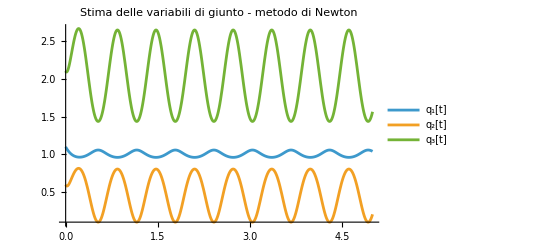

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "1",λ,μ, "Stima delle variabili di giunto - metodo di Newton","Traiettoria ideale e reale end effector - metodo di Newton"];
res[[1]]
res[[2]]
```

### Metodo del gradiente

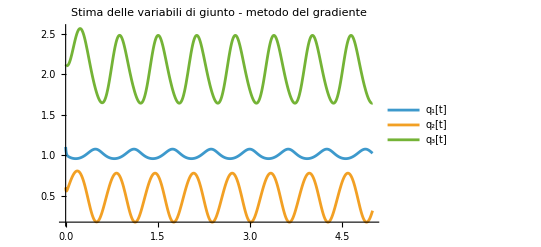

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "2",λ,μ, "Stima delle variabili di giunto - metodo del gradiente","Traiettoria ideale e reale end effector - metodo del gradiente"];
res[[1]]
res[[2]]
```

### Metodo misto

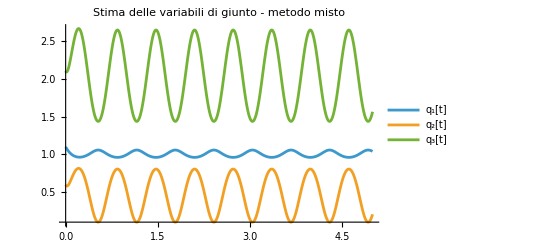

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "3",λ,μ, "Stima delle variabili di giunto - metodo misto","Traiettoria ideale e reale end effector - metodo misto"];
res[[1]]
res[[2]]
```

## Energia cinetica

```mathematica
xyz={{0,-Subscript[L, 1]/2,0},{-Subscript[L, 2]/2,0,0},{0,0,-Subscript[L, 3]/2}};
tab2=Join[tab,xyz,2];
TableForm[tab2,TableHeadings->{{"1","2","3"},{"θ","d","α","a","x","y","z"}}]
```

| θ | d | α | a | x | y | z
1 | q_1 | L_1 | π/2 | 0 | 0 | -L_1/2 | 0
2 | q_2 | 0 | π/2 | L_2 | -L_2/2 | 0 | 0
3 | 0 | q_3 | 0 | 0 | 0 | 0 | -L_3/2

```mathematica
{T,U}=energiaRobot[tab2,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}];
```

Link1

B_ω  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B_t  (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

T_1  1/2 I_(1y) (q_1')^2

T_2  0

T  1/2 I_(1y) (q_1')^2

U  4.905 m_1 L_1

Link2

B_ω  (c_2^2 I_(2z)+I_(2x) s_2^2 | 0 | 0
0 | I_(2y) | 0
0 | 0 | 0)

B_t  (1/4 c_2^2 m_2 L_2^2 | 0 | 0
0 | 1/4 m_2 L_2^2 | 0
0 | 0 | 0)

B  (I_(2x) s_2^2+1/4 c_2^2 (4 I_(2z)+m_2 L_2^2) | 0 | 0
0 | I_(2y)+1/4 m_2 L_2^2 | 0
0 | 0 | 0)

T_1  1/2 ((c_2^2 I_(2z)+I_(2x) s_2^2) (q_1')^2+I_(2y) (q_2')^2)

T_2  1/8 m_2 L_2^2 (c_2^2 (q_1')^2+(q_2')^2)

T  1/8 ((4 I_(2x) s_2^2+c_2^2 (4 I_(2z)+m_2 L_2^2)) (q_1')^2+(4 I_(2y)+m_2 L_2^2) (q_2')^2)

U  9.81 m_2 (L_1+(s_2 L_2)/2)

Link3

B_ω  (c_2^2 I_(3z)+I_(3x) s_2^2 | 0 | 0
0 | I_(3y) | 0
0 | 0 | 0)

B_t  (1/4 m_3 (-2 c_2 L_2+s_2 (L_3-2 q_3))^2 | 0 | 0
0 | 1/4 m_3 (4 L_2^2+(L_3-2 q_3)^2) | -m_3 L_2
0 | -m_3 L_2 | m_3)

B  (c_2^2 I_(3z)+I_(3x) s_2^2+1/4 m_3 (-2 c_2 L_2+s_2 (L_3-2 q_3))^2 | 0 | 0
0 | I_(3y)+1/4 m_3 (4 L_2^2+(L_3-2 q_3)^2) | -m_3 L_2
0 | -m_3 L_2 | m_3)

T_1  1/2 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)

T_2  1/8 m_3 ((-2 c_2 L_2+s_2 (L_3-2 q_3))^2 (q_1')^2+4 q_3' (-L_2 q_2'+q_3')+q_2' ((4 L_2^2+(L_3-2 q_3)^2) q_2'-4 L_2 q_3'))

T  1/8 (4 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)+m_3 ((-2 c_2 L_2+s_2 (L_3-2 q_3))^2 (q_1')^2+4 q_3' (-L_2 q_2'+q_3')+q_2' ((4 L_2^2+(L_3-2 q_3)^2) q_2'-4 L_2 q_3')))

U  9.81 m_3 (L_1+s_2 L_2+1/2 c_2 (L_3-2 q_3))

Risultati

Energia cinetica totale  1/8 ((4 I_(1y)+4 I_(2x) s_2^2+c_2^2 (4 I_(2z)+m_2 L_2^2)) (q_1')^2+(4 I_(2y)+m_2 L_2^2) (q_2')^2+4 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)+m_3 ((-2 c_2 L_2+s_2 (L_3-2 q_3))^2 (q_1')^2+4 q_3' (-L_2 q_2'+q_3')+q_2' ((4 L_2^2+(L_3-2 q_3)^2) q_2'-4 L_2 q_3')))

Energia potenziale gravitazionale totale  4.905 m_1 L_1+m_2 (9.81 L_1+4.905 s_2 L_2)+9.81 m_3 (L_1+s_2 L_2+1/2 c_2 (L_3-2 q_3))

## Eulero Lagrange

```mathematica
F=1/2*{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'}.DiagonalMatrix[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3]}].{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'};
euleroLagrange[T,U,F,{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}]//TableForm
```

f_1 q_1'+1/4 (4 Sin[2 q_2] (I_(3x)-I_(3z)) q_1' q_2'+Sin[2 q_2] (4 I_(2x)-4 I_(2z)-m_2 L_2^2) q_1' q_2'+2 m_3 (-2 Cos[q_2] L_2+Sin[q_2] (L_3-2 q_3)) q_1' (Cos[q_2] (L_3-2 q_3) q_2'+2 Sin[q_2] (L_2 q_2'-q_3'))+4 (Sin[q_2]^2 I_(3x)+Cos[q_2]^2 I_(3z)) q_1''+(4 I_(1y)+4 Sin[q_2]^2 I_(2x)+Cos[q_2]^2 (4 I_(2z)+m_2 L_2^2)) q_1''+m_3 (-2 Cos[q_2] L_2+Sin[q_2] (L_3-2 q_3))^2 q_1'')==u_1
1/8 (4 Sin[2 q_2] (-I_(2x)+I_(2z)-I_(3x)+I_(3z)) (q_1')^2+8 f_2 q_2'+8 (I_(2y)+I_(3y)) q_2''+m_2 L_2 (39.24 Cos[q_2]+L_2 (1. Sin[2 q_2] (q_1')^2+2 q_2''))+m_3 (Sin[q_2] (-39.24 L_3+78.48 q_3)+(L_3-2 q_3) (-8 q_2' q_3'-(L_3-2 q_3) (Sin[2 q_2] (q_1')^2-2 q_2''))+4 L_2^2 (Sin[2 q_2] (q_1')^2+2 q_2'')+L_2 (78.48 Cos[q_2]+4 Cos[2 q_2] (L_3-2 q_3) (q_1')^2-8 q_3'')))==u_2
f_3 q_3'+1/2 m_3 (-19.62 Cos[q_2]+(L_3-2 q_3) (Sin[q_2]^2 (q_1')^2+(q_2')^2)-L_2 (Sin[2 q_2] (q_1')^2+2 q_2'')+2 q_3'')==u_3